#### Задание 13

Решить задачу дискретной оптимизации методом ветвей и границ

```mathematica
f=4 Subscript[x, 1]+6 Subscript[x, 2];
```

```mathematica
constraints={
5 Subscript[x, 1]-2 Subscript[x, 2]>=10.2,
-2 Subscript[x, 1]+Subscript[x, 2]<=5,
3 Subscript[x, 2]<=3.5,
Subscript[x, 1]+Subscript[x, 2]<=3.9
};
```

```mathematica
P={Subscript[x, 1]>=0,Subscript[x, 2]>=0};
```

```mathematica
X={Subscript[x, 1],Subscript[x, 2]};
```

Решение исходной задачи (не целочисленное)

```mathematica
Maximize[{f,constraints,P},X]
```

{17.9333,{x_1→2.73333,x_2→1.16667}}

```mathematica
Maximize[{
f,constraints,P,
Subscript[x, 1]<=2
},X]
```

NMaximize::nsol: There are no points that satisfy the constraints {5 x_1-2 x_2≥10.2,-2 x_1+x_2≤5,3 x_2≤3.5,x_1+x_2≤3.9,x_1≥0,x_2≥0,x_1≤2}.

Maximize::infeas: The problem is infeasible.

{-∞,{x_1→Indeterminate,x_2→Indeterminate}}

```mathematica
Maximize[{
f,constraints,P,
Subscript[x, 1]>=3
},X]
```

{17.4,{x_1→3.,x_2→0.9}}

```mathematica
Maximize[{
f,constraints,P,
Subscript[x, 1]>=3,
Subscript[x, 2]<=0
},X]
```

{15.6,{x_1→3.9,x_2→0.}}

```mathematica
Maximize[{
f,constraints,P,
Subscript[x, 1]>=3,
Subscript[x, 2]<=0,
Subscript[x, 1]<=3
},X]
```

{12.,{x_1→3.,x_2→0.}}

```mathematica
Maximize[{
f,constraints,P,
Subscript[x, 2]<=0,
Subscript[x, 1]>=4
},X]
```

NMaximize::nsol: There are no points that satisfy the constraints {5 x_1-2 x_2≥10.2,-2 x_1+x_2≤5,3 x_2≤3.5,x_1+x_2≤3.9,x_1≥0,x_2≥0,x_2≤0,x_1≥4}.

Maximize::infeas: The problem is infeasible.

{-∞,{x_1→Indeterminate,x_2→Indeterminate}}

```mathematica
Maximize[{
f,constraints,P,
Subscript[x, 1]>=3,
Subscript[x, 2]>=1
},X]
```

NMaximize::nsol: There are no points that satisfy the constraints {5 x_1-2 x_2≥10.2,-2 x_1+x_2≤5,3 x_2≤3.5,x_1+x_2≤3.9,x_1≥0,x_2≥0,x_1≥3,x_2≥1}.

Maximize::infeas: The problem is infeasible.

{-∞,{x_1→Indeterminate,x_2→Indeterminate}}

Проверка:

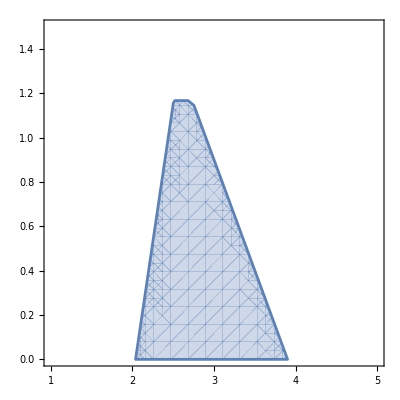

```mathematica
RegionPlot[And@@Join[constraints,P],{Subscript[x, 1],1,5},{Subscript[x, 2],0,1.5}]
```

```mathematica
Maximize[{f,constraints,P},X,Integers]
```

{12.,{x_1→3,x_2→0}}